```mathematica
generateExpBarCharts[Variance_]:=Module[{centralIdealData,centralNoisyData,distrNoisyData,CIAvgs,CISDevs,CNAvgs,CNSDevs,DNAvgs,DNSDevs,makePlot,errorBar,chartData,CIData,CNData,DNData},

errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}];
makePlot[data_,title_]:=BarChart[data,ChartElementFunction->errorBar["Rectangle"],PlotLabel->title,(*ChartLayout-> "Stacked",*)BarSpacing->{0,.5},ChartLabels->{{Framed["Cen. Ideal",FrameMargins-> 20],"Cen. Noisy","Distr. Noisy"}, None},ChartLegends-> Placed[{"Attempted","Failed"},Right],BaseStyle->FontSize->18,ImageSize-> {500,300}];

centralIdealData=<<("C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_"<>ToString[Variance]<>"_Data\\CentralIdealExpLog_ExpVariance_"<>ToString[Variance]<>".txt");
centralNoisyData=<<("C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_"<>ToString[Variance]<>"_Data\\CentralNoisyExpLog_ExpVariance_"<>ToString[Variance]<>".txt");
distrNoisyData=<<("C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_"<>ToString[Variance]<>"_Data\\DistrNoisyExpLog_ExpVariance_"<>ToString[Variance]<>".txt");

CIAvgs=Mean[centralIdealData⟦2;;101⟧];
CISDevs=StandardDeviation[centralIdealData⟦2;;101⟧];
CNAvgs=Mean[centralNoisyData⟦2;;101⟧];
CNSDevs=StandardDeviation[centralNoisyData⟦2;;101⟧];
DNAvgs=Mean[distrNoisyData⟦2;;101⟧];
DNSDevs=StandardDeviation[distrNoisyData⟦2;;101⟧];

CIData=Table[CIAvgs⟦i⟧->CISDevs⟦i⟧,{i,1,Length[CIAvgs]}];
CNData=Table[CNAvgs⟦i⟧->CNSDevs⟦i⟧,{i,1,Length[CNAvgs]}];
DNData=Table[DNAvgs⟦i⟧->DNSDevs⟦i⟧,{i,1,Length[DNAvgs]}];

Row[{
makePlot[{CIData⟦3;;4⟧,CNData⟦3;;4⟧,DNData⟦3;;4⟧},"Target Data (Central Noise σ="<>ToString[Variance]<>")"],
makePlot[{CIData⟦5;;6⟧,CNData⟦5;;6⟧,DNData⟦5;;6⟧},"Agent Data (Central Noise σ="<>ToString[Variance]<>")"]
}]
]
```

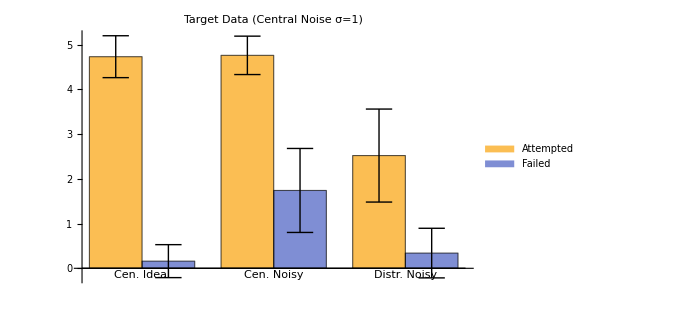
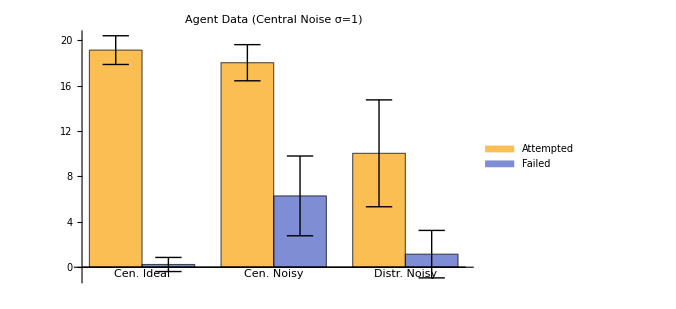
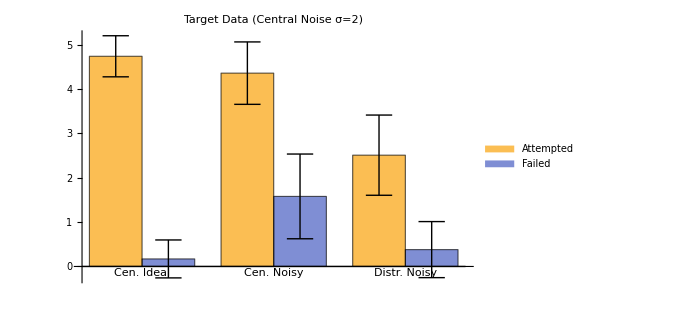
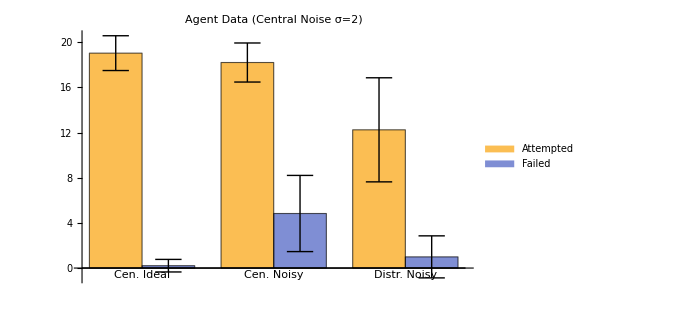
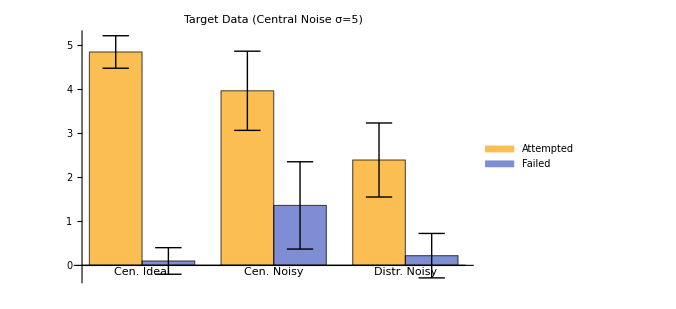
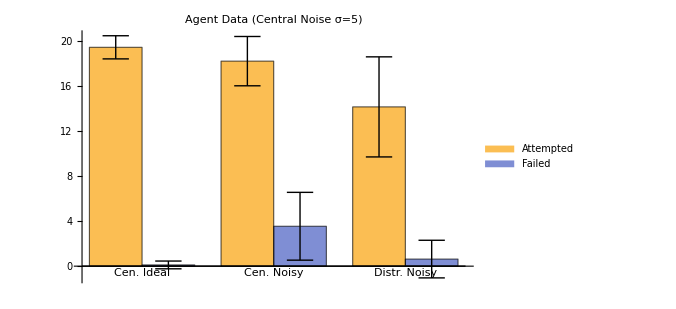

```mathematica
Column[{generateExpBarCharts[1],generateExpBarCharts[2],generateExpBarCharts[5]}]
```

```mathematica
BarChart
```